# Analyzing the Effect of Mass, Friction and Spring Constant on the Step Response of a Second-Order System

By changing the parameters of a second order system its step response is calculated and graphically displayed

Jaime Buitrago, Jun. 24,  2018

The study of system dynamics requires great insight in the behavior of a system to different inputs.  The step response in particular provides a clear picture of the nature of the system.  It is simple to determine if a system has a lot of inertia or very little, if there will be oscillations, if the oscillations are dampened, etc.  By providing a simple interface, this project attempts to enable a student to play with the system parameters mass, friction coefficient and spring constant to see the effects on the system response.

## Model Description

A simplified spring-mass-damper model is shown below

USE IMPORT FOR THIS FIGURE

The parameters of the system are: Mass m in kg, Spring Constant k in N/m, and Friction Coefficient b in N/m/s.  The system dynamics are represented by the equation

F = m a + b v + kx

Where a is the acceleration, v is the velocity, and x is the displacement.  In transfer function form, the relationship between the output and the input is given by the function trans.

The TransferFunctionModel creates an object from the Laplace transform of the system equation in frequency domain:

```mathematica
trans[m_,b_,k_]:=TransferFunctionModel[{{1/(m s^2 + b s + k)}},s]
```

If, for example, our parameters were, in kg, N/m, and N/m/s respectively,

```mathematica
m= 2; 
b = 1;
c = .5;
```

We could visualize the transfer function form of the system as

```mathematica
sampleSystem=trans[m,b,c]
```

1/(0.5+s+2 s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1110.51FalseFalseFalseAutomaticNoneAutomatic

## Step Response

The step response is the response of the system to a force that has an instantaneous change from 0 to 1 N (a unit step) in time t = 0s.  the input force graph looks like:

STEP INPUT GRAPH HERE

For the sample system, the step response can be calculated as:

```mathematica
stepResp=OutputResponse[sampleSystem,UnitStep[t],t]
```

{1/2 ⅇ^(-0.25 t) ((-4.+2.22045×10^-16 ⅈ) Cos[0.433013 t] UnitStep[t]+(4.-2.22045×10^-16 ⅈ) 2.71828^(0.25 t) Cos[0.433013 t]^2 UnitStep[t]+2.46519×10^-32 ⅇ^(0.25 t) Cos[0.433013 t]^2 UnitStep[t]-(2.3094+2.46519×10^-32 ⅈ) Sin[0.433013 t] UnitStep[t]+(1.33227×10^-15+1.28198×10^-16 ⅈ) 2.71828^(0.25 t) Cos[0.433013 t] Sin[0.433013 t] UnitStep[t]-(7.69185×10^-16-2.46519×10^-32 ⅈ) ⅇ^(0.25 t) Cos[0.433013 t] Sin[0.433013 t] UnitStep[t]-(1.33333+0. ⅈ) 2.71828^(0.25 t) Sin[0.433013 t]^2 UnitStep[t]+(5.33333-2.56395×10^-16 ⅈ) ⅇ^(0.25 t) Sin[0.433013 t]^2 UnitStep[t])}

As we can see, the analytical solution to this system is quite complex.  We can see a graph of the step response of the system as follows:

IMPROVE THIS GRAPH

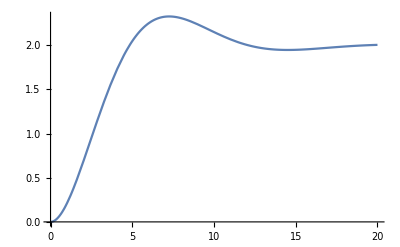

```mathematica
Plot[stepResp,{t,0,20}]
```

## Influence of System Parameters

What happens if the mass of the system changes?  Does an increase in mass have an influence on the system response?  We can analyze the influence of each parameter in the step response by changing the parameters of the model

Manipulate will create a graph that allows us to change the variables of the system by using sliders:

```mathematica
Manipulate[stepRes=OutputResponse[trans[m,b,k],UnitStep[t],t];Plot[stepRes,{t,1,20},Frame->True,PlotRange->All,GridLines->Automatic],{{m,.5},.1,1},{{b,.5},0,1,.1},{{k,.5},0,1,.1}]
```

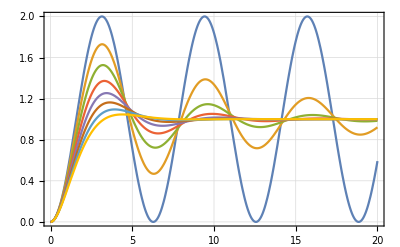

```mathematica
Plot[Evaluate@Table[Tooltip[OutputResponse[trans[1,b,1],UnitStep[t],t],b],{b,Range[0,1.4,0.2]}],{t,0,20},Frame->True,PlotRange->All,GridLines->Automatic]
```

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)